## Set up

```mathematica
nrep=3;
```

```mathematica
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
hd="/Users/keitokiddo/VC_revision/Simulations/";
fl="4_8_DEN";
wd=StringJoin[hd,fl];
SetDirectory[wd];
```

```mathematica
alpha=4;(* alleles per site *)
l=8;(* length of sequence *)
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
```

```mathematica
wt=ConstantArray[0,l];
AA={"A","C","G","T"};
AAtoDigitRules = {"A"->0,"C"->1,"G"->2,"T"->3};
DigitToAARules = {0->"A",1->"C",2->"G",3->"T"};
sequencesAA=StringJoin[#/.DigitToAARules]&/@sequences;
wtAA = sequencesAA[[1]]
```

AAAAAAAA

```mathematica
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
MakeLapRec[alpha_,l_]:=Module[{L1,L,m},
L1 = SparseArray[alpha*IdentityMatrix[alpha] - ArrayReshape[ConstantArray[1,alpha^2],{alpha,alpha}]];
m=1;
L=L1;
While[m<l, L = KroneckerProduct[L, IdentityMatrix[alpha]] + KroneckerProduct[IdentityMatrix[alpha^m],L1];
m++];
L
]
L=MakeLapRec[alpha,l];//AbsoluteTiming
```

{2.2973,Null}

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

#### Export design matrix for glmnet

```mathematica
(*varall = ConstantArray[0, alpha^l];*)
```

```mathematica
(*designAllonehot=s2donehot[sequences,Range[0,l]];//AbsoluteTiming*)
```

```mathematica
(*rules=Flatten[Table[Join[Table[designrules[sequences[[j]],k,wt,j],{k,3}]],{j,Length[sequences]}],2];
null3=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*(alpha - 1)^k,{k,0,3}]}];
Export["data/rules.tsv",Transpose@{Most[ArrayRules[null3]][[All,1]][[All,1]],Most[ArrayRules[null3]][[All,1]][[All,2]]},"TSV"];*)
```

#### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
```

#### Import training samples

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,Length@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

## *Functions

### Basic functions

```mathematica
dp[v_]:=v//DeleteDuplicates
uqc[v_]:=v//DeleteDuplicates//Length
lg[v_]:=v//Length
dim[m_]:=m//Dimensions
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules]
```

```mathematica
associate0[list_,obj_]:=Table[list[[i]]->obj,{i,Length[list]}]
```

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
ginv[x_]:=If[N[x]==0.,0,1/x]
```

```mathematica
r2[x_, y_] := If[Length@x<2, {}, Correlation[x, y]^2];


mse[x_, y_] := Mean[(x - y)^2];
maxorder[list_] := 
  Module[{i}, 
   For[i = 1, list[[i ;;]] != ConstantArray[0, Length[list[[i ;;]]]], 
    i++]; i - 1];

(*From sequence to lexicographical position*)

seq2pos[seq_] := FromDigits[seq, alpha] + 1

(*Map a vector of length m to a vector of length alpha^l. "list" contains the lexicographical positions for all sequences in "data"*)MapPartialVal[list_,data_,height_]:=Module[{Ab},Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];Ab.data]
```

### Projection operators

```mathematica
Pby[x_,Pcoeffs_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];
```

```mathematica
Pkby[x_,k_]:=Module[{Pcoeffs},Pcoeffs=Inverse[LPs].wkd[[All,k+1]];Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1]];
```

### Regression functions

```mathematica
(*Ridge regression with regularization parameter "Î»" and design matrix "design"*)

RidgeRegression[design_, response_, Î»_] := Module[{cross},
  cross = Transpose[design].design;
  Do[cross[[i, i]] += Î»^2, {i, Length[cross]}];
  LinearSolve[cross,
   Transpose[design].response,
   Method -> {"Krylov", "Method" -> "ConjugateGradient", 
     "Preconditioner" -> "ILU0"}]]

(*Ordinary least square regression*)

OrdinaryRegression[design_, response_] := Module[{cross},
  cross = Transpose[design].design;
  LinearSolve[cross, Transpose[design].response, Method -> "Krylov"]]

(*Build design vector for a sequence using the Taylor encoding*)

s2dTaylor[seq_, order_, wt_] := Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order) & /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha - 1)^order}]
  ]
(*Build design vector for sequence using the one-hot encoding*)

s2d[seq_, order_] := Module[{sub1, sub2, pos},
  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#], alpha] + 
      1 + (#[[1]] - 1)*(alpha^order) & /@ sub2;
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha)^order}]
  ]

designrules[seq_, order_, wt_,j_]:=Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order)+ Total@Table[Binomial[l,k](alpha-1)^(k),{k,0,order-1}]& /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
s2dTaylor2[seqs_,order_,wt_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrules[seqs[[j]],k,wt,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha - 1)^k,{k,order}]}]]
```

### Kernelized regressions

```mathematica
CIby[x_]:={0,-alpha/2,1/2}.NestList[L.#&,x,2](*Similar to C.f, we implement multiplication by a matrix that can be expressed as a polynomial in L using NestList.*)(*coeffsinLn: vector of coefficients for L^n*)
SprsinLnBy[x_,coeffsinLn_]:=coeffsinLn[[1;;maxorder[coeffsinLn]]].NestList[L.#&,x,maxorder[coeffsinLn]-1](*Apply the locally non-epistatic smoother M to a vector*)
Smooth[x_]:=-(1/(Binomial[l,2](alpha-1)^2))CIby[x]+x(*Calculate the average squared epistasic coefficient for a vector x*)
Cnorm[x_]:=(1/(nfaces))x.CIby[x]
```

```mathematica
(*Multiplication by the C matrix defined in the main text. For the matrix by vector multiplication C.f, we evaluate it as {0,-alpha/2,1/2}.{f,L.f,L.L.f} using the function NestList. Note that we have omitted the constant 1/s, since it does not affect the solution to the linear equation*)
(*Minimum epistasis interpolation solver*)
Cinterp[training_,y_]:=Module[{Ai,Ab},Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],training],Range[1,alpha^l-Length[training]]}]->1,{alpha^l,alpha^l-Length[training]}];Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];(Ai.LinearSolve[Transpose[Ai].CIby[Ai.#]&,-Transpose[Ai].CIby[Ab.y],Method->{"Krylov",Method->"ConjugateGradient",Tolerance->10^-15}])+Ab.y](*Regularized regression with regularization parameter given by "rp". "Ccoeffs" and "Pcoeffs" contain entries for a general cost matrix C (not necessarily the C used in the minimum epistasis interpolation problem) and projection matrix P each of which is represented as the coefficients of a polynomial in L. "Ccoeffs" and "Pcoeffs" for fitting models of different orders are defined below*)
Creg[Ccoeffs_,Pcoeffs_,training_,data_,rp_,var_,startingvector_]:=Module[{Ab,W,Cby,Pby},W=(1/Length[data]) SparseArray[Table[{training[[i]],training[[i]]}->(1/var[[i]]),{i,Length[training]}],{alpha^l,alpha^l}];Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];Cby[x_]:=rp*Ccoeffs[[1;;maxorder[Ccoeffs]]].NestList[L.#&,x,maxorder[Ccoeffs]-1];Pby[x_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];LinearSolve[(Cby[#]+Pby[W.Pby[#]])&,Pby[W.Ab.data],Method->{"Krylov",Method->"ConjugateGradient","StartingVector"->If[Length[startingvector]==0,ConstantArray[0,alpha^l],startingvector]}]]

(*10-fold crossvalidation using the function Creg*)CrossvalidationC[Ccoeffs_,Pcoeffs_,list_,response_,rps_,variance_,fold_,rep_]:=Module[{size,subsets,r,rpsr},
size=Ceiling[Length[response]/fold]; 
subsets=Partition[RandomSample[Range[1,Length[response]]],size,size,1,{}];r=Table[Table[{},Length[rps]+1],rep];Do[Do[r[[k]][[i+1]]=Creg[Ccoeffs,Pcoeffs,list[[Flatten[Drop[subsets,{k}]]]],response[[Flatten[Drop[subsets,{k}]]]],rps[[i]],variance[[Flatten[Drop[subsets,{k}]]]],{}],{i,Length[rps]}],{k,rep}];Table[mse[r[[k]][[i+1]][[list[[subsets[[k]]]]]],response[[subsets[[k]]]]]
,{k,rep},{i,Length[rps]}]
]

(*Extract best regularization parameter from the crossvalidation outputs*)CV[mse_,rps_]:=Module[{means,ses,min,bestlambda},means=Mean[mse];ses=If[Dimensions[mse][[1]]>1,StandardDeviation[mse]/√(Dimensions[mse][[1]]),ConstantArray[0,Dimensions[mse][[2]]]];min=First[Ordering[means]];bestlambda=rps[[min ]];{bestlambda,means,ses}]
```

### Matrix coefficients

```mathematica
(*Krawtchouk polynomial*)
w[alpha_, k_, d_] := alpha^(-l) ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[alpha,k,d],{d,0,l},{k,0,l}];
```

```mathematica
(*LPs contains entries of L^n defined at d=0,1,...l. For any matrix whose (i,j)-th entry only depends on d(i,j), we can then solve a linear equation for the coefficients*)
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;

(*Entries of the pseudo-inverse of the interpolation matrix C*)
KIentries=Table[ReleaseHold[Hold[∑_(k=2)^length (alpha^(-l)  1/(((a k)^2-a(a k))a^length)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for pairwise regression*)
C2entries=Table[ReleaseHold[Hold[∑_(k=2)^2 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for three-way regression*)
C3entries=Table[ReleaseHold[Hold[∑_(k=2)^3 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Entries of the cost matrix for the Additive model*)
P1entries=Table[ReleaseHold[Hold[∑_(k=0)^1 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Pairwise model*)
P2entries=Table[ReleaseHold[Hold[∑_(k=0)^2 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Three-way model*)
P3entries=Table[ReleaseHold[Hold[∑_(k=0)^3 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Coefficients for the interpolation matrix C in L*)
CIinLn=PadRight[{0,-alpha/2,1/2},l+1];

(*Coefficients for the interpolation kernel matrix K in L*)
KIinLn=Inverse[LPs].KIentries;

(*Coefficients for the cost matrix for the Pairwise model in L*)
C2inLn=Inverse[LPs].C2entries;

(*Coefficients for the cost matrix for the Three-way model in L*)
C3inLn=Inverse[LPs].C3entries;

(*Coefficients for the projection matrix for the Three-way model in L*)
P3inLn=Inverse[LPs].P3entries;

(*Coefficients for the projection matrix for the Pairwise model in L*)
P2inLn=Inverse[LPs].P2entries;

(*Coefficients for the projection matrix for the Additive model in L*)
P1inLn=Inverse[LPs].P1entries;
```

### Build matrices

```mathematica
(*(*Build graph Laplacian of the sequence space. L is a sparse matrix with sparsity = 1 - ((alpha-1)l+1)/(alpha^l). Therefore we'll use it to facilitate fast solution of most linear equations in this notebook*)
MakeLaplacian[A_,l_]:=SparseArray[Join[ParallelTable[{i,i}->l(A-1),{i,1,A^l}],Flatten[ParallelTable[{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]*)
```

```mathematica
(*AbsoluteTiming[L=MakeLaplacian[alpha,l];]*)
```

```mathematica
(*MakeAdj[A_,l_]:=SparseArray[Flatten[ParallelTable[{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->1,{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]*)
```

```mathematica
(*Adj=MakeAdj[alpha,l];//AbsoluteTiming*)
```

```mathematica
(*Adj = -(L - SparseArray[Flatten[Table[{i,i}->(alpha-1)*l,{i,1,alpha^l}],2]]);*)
```

```mathematica
(*null = Table[
   Join[s2dTaylor[sequences[[i]], 0, wt], 
    s2dTaylor[sequences[[i]], 1, wt]], {i, Length[sequences]}];//AbsoluteTiming*)
```

```mathematica
(*null2=SparseArray[Table[Join[s2dTaylor[seq,0,wt],s2dTaylor[seq,1,wt],s2dTaylor[seq,2,wt]],{seq,sequences}]];//AbsoluteTiming*)
```

```mathematica
designrulesonehot[seq_, order_,j_]:=Module[{ sub1, sub2, pos},

  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] , alpha ] + 
      1 + (#[[1]]-1 )*((alpha )^order)+ Total@Table[Binomial[l,k](alpha)^(k),{k,0,order-1}]& /@ 
    sub2;
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
s2donehot[seqs_,order_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrulesonehot[seqs[[j]],k,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha ^k),{k,order}]}]]
```

```mathematica
rules=Flatten[Table[Join[Table[designrulesonehot[sequences[[j]],k,j],{k,0, 1}]],{j,Length[sequences]}],2];//AbsoluteTiming
```

{6.16834,Null}

```mathematica
nullonehot=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*(alpha)^k,{k,0,1}]}];
```

## Python prep

Export data to Python for later analyses

import os

fl_name = "4_8_DEN"
alpha, l = 4, 8

os.chdir("/Users/keitokiddo/VC_revision/Simulations/" + fl_name)
import scipy as sp
import sys
sys.path.insert(1, '/Users/keitokiddo/git/vcregression/vcregression')

import vc_regression as vc
import itertools
import os
import csv
import pandas as pd
import numpy as np
import arrow
import scipy as sp

#define sequence space parameters
alpha, l = 4, 8 #alpha: alphabet size; l: sequence length
G = alpha**l
bases = np.array(range(alpha))
seqs = list(itertools.product(bases, repeat=l)) #generate all possible sequences

dirin = "data/"
dirout = "out/"
vc.preliminary_preparation(alpha, l)

Loading L_sparse ...

0.05 sec

## Simulate

### Well defined random field with exponential lambdas

```mathematica
lambdas=Nbyfirst@Table[2^(l-i) (1 + (alpha-1)*.5)^(l-i),{i,0,l}]
```

{1.,0.2,0.04,0.008,0.0016,0.00032,0.000064,0.0000128,2.56×10^-6}

```mathematica
Export[StringJoin["data/","lambdas",".tsv"],lambdas,"TSV"];
```

```mathematica
VCExpected=Nbysum[Rest@mks*Rest@lambdas]//N
```

{0.114423,0.240288,0.288346,0.216259,0.103804,0.0311413,0.00533851,0.000400388}

```mathematica
fs=Table[{},nrep];
```

```mathematica
Do[
f=RandomVariate[NormalDistribution[],alpha^l];f=Table[Sqrt[(lambdas[[k+1]]mks[[k+1]]/Norm[Pkby[f,k]]^2)]Pkby[f,k],{k,0,l}]//Total;
fs[[i]]=f,
{i, nrep}]
```

```mathematica
Table[Norm[Pkby[f,k]]^2/mks[[k+1]],{k,0,l}]-lambdas
```

{-1.03695×10^-12,-2.68119×10^-14,-2.14134×10^-14,-1.04396×10^-14,-4.49337×10^-15,-6.26734×10^-15,-7.22436×10^-15,-7.54508×10^-15,-6.97794×10^-15}

```mathematica
Do[Export[StringJoin["data/",fl,"_f_",ToString[i],".tsv"],fs[[i]],"TSV"],{i,nrep}]
```

### Noised FL

```mathematica
Variance[fs[[1]]//Flatten]
```

0.000640111

```mathematica
varnoise = .25 * Variance[fs[[1]]//Flatten]
```

0.000160028

```mathematica
noisevecs = Table[RandomVariate[NormalDistribution[0, Sqrt[varnoise]], alpha^l], nrep];
```

```mathematica
noisevecs[[1]]//Norm
```

3.2346

```mathematica
noisevecs[[1]]//Variance
```

0.000159649

```mathematica
fs[[1]]//Variance
```

0.000640111

```mathematica
fns = fs + noisevecs;
```

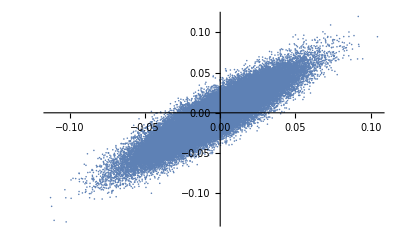

0.800427

```mathematica
ListPlot[Transpose@{fs[[1]], fns[[1]]},PlotRange->All]
r2[fs[[1]], fns[[1]]]
```

```mathematica
Do[Export[StringJoin["data/",fl,  "_f_","noised_", ToString[i],".tsv"],fns[[i]],"TSV"],{i,nrep}];
```

## Generate training samples

### Random sampling

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
trs=Table[RandomSample[Range[Length[sequences]],samplesizes[[i]]],{i,Length[samplesizes]}];
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
Do[Export[StringJoin[ "data/", "tr_",ToString[i],".tsv"],trs[[i]],"TSV"],{i,lg@trs}];
```

### Simulated mutagenesis

```mathematica
wt=ConstantArray[0,l];
```

```mathematica
wg=mks^(-1)//N
```

{1.,0.0416667,0.00396825,0.000661376,0.000176367,0.0000734862,0.0000489908,0.0000571559,0.000152416}

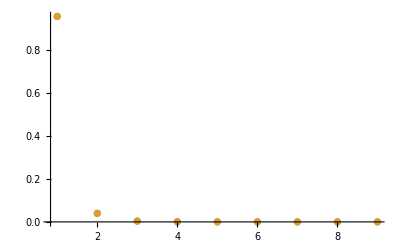

```mathematica
ListPlot[{Nbysum[mks^-1],Nbysum[wg]},PlotRange->All]
```

```mathematica
(*If no seq left in distance class, We randomly choose one to exclude in the training set*)
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
weights=hd/.associate[Range[0,l],wg];
```

ReplaceAll::reps: {associate[{0,1,2,3,4,5,6,7,8},{1.,0.0416667,0.00396825,0.000661376,0.000176367,0.0000734862,0.0000489908,0.0000571559,0.000152416}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,lg@seqsbyD}];
```

```mathematica
p=.1;
weights=(1-p)^(-#+l) p^# &/@hd;
```

```mathematica
(*We give minimum epistasis interpolation 1%, 10%, 50% and 90% of all data as training and use the rest of the data as test*)
trsmut=Table[RandomSample[weights->Range[alpha^l],Ceiling[i alpha^l]],{i,proportions}];
tstmut=Table[Complement[Range[alpha^l],trsmut[[i]]]//Flatten,{i,Length[proportions]}];
```

```mathematica
proportions//N
```

{0.00999451,0.0500031,0.100006,0.199997,0.300003,0.399994,0.5,0.600006,0.699997,0.800003,0.899994,0.949997,0.990005}

```mathematica
SortBy[hd[[trsmut[[1]]]]//Tally,First]
%[[All,2]]/mks[[;;Length[%]]]//N
```

{{0,1},{1,24},{2,212},{3,265},{4,105},{5,42},{6,5},{8,1}}

{1.,1.,0.84127,0.175265,0.0185185,0.00308642,0.000244954,0.0000571559}

```mathematica
Do[Export[StringJoin["data/", "tr_mut_",ToString[i],".tsv"],trsmut[[i]],"TSV"],{i,lg@trsmut}];
```

## VC

#### Random sampling

varall = 0*np.ones(G)

f = 'f'
train = 'tr'
scheme = 'random'


for i in range(3):
    for j in range(13):
        name = [fl_name, f, str(i + 1)]
        tr_name = [train, str(j + 1)]
        map_name = [fl_name, scheme, "vc", str(i + 1), str(j + 1)]
        lda_name = [fl_name, scheme, "lda", str(i + 1), str(j + 1)]
        response = pd.read_csv(dirin + "_".join(name) + ".tsv", header = None)
        response = response.to_numpy()
        response = response.squeeze()
        print("working on sample " + str(i+1) + "," + str(j+1))
        tr = pd.read_csv(dirin + "_".join(tr_name) + ".tsv", header = None)
        tr = np.array(tr).flatten()
        tr -= 1
        lambdas,map = vc.compute_posterior_mean_ex(np.array(seqs)[tr], np.array(response)[tr], np.array(varall)[tr])
        pd.DataFrame(map).to_csv(dirout + "_".join(map_name) + ".tsv", header = None, index = None)
        pd.DataFrame(lambdas).to_csv(dirout + "_".join(lda_name) + ".tsv", header = None, index = None)

working on sample 1,1

working on sample 1,2

working on sample 1,3

working on sample 1,4

working on sample 1,5

working on sample 1,6

working on sample 1,7

working on sample 1,8

working on sample 1,9

working on sample 1,10

working on sample 1,11

working on sample 1,12

working on sample 1,13

working on sample 2,1

working on sample 2,2

working on sample 2,3

working on sample 2,4

working on sample 2,5

working on sample 2,6

working on sample 2,7

working on sample 2,8

working on sample 2,9

working on sample 2,10

working on sample 2,11

working on sample 2,12

working on sample 2,13

working on sample 3,1

working on sample 3,2

working on sample 3,3

working on sample 3,4

working on sample 3,5

working on sample 3,6

working on sample 3,7

working on sample 3,8

working on sample 3,9

working on sample 3,10

working on sample 3,11

working on sample 3,12

working on sample 3,13

#### Noised landscape

varall = 0.000160028*np.ones(G)

f = 'f_noised'
train = 'tr'
scheme = 'noised'


for i in range(3):
    for j in range(13):
        name = [fl_name, f, str(i + 1)]
        tr_name = [train, str(j + 1)]
        map_name = [fl_name, scheme, "vc", str(i + 1), str(j + 1)]
        lda_name = [fl_name, scheme, "lda", str(i + 1), str(j + 1)]
        response = pd.read_csv(dirin + "_".join(name) + ".tsv", header = None)
        response = response.to_numpy()
        response = response.squeeze()
        print("working on sample " + str(i+1) + "," + str(j+1))
        tr = pd.read_csv(dirin + "_".join(tr_name) + ".tsv", header = None)
        tr = np.array(tr).flatten()
        tr -= 1 
        lambdas,map = vc.compute_posterior_mean_ex(np.array(seqs)[tr], np.array(response)[tr], np.array(varall)[tr])
        pd.DataFrame(map).to_csv(dirout + "_".join(map_name) + ".tsv", header = None, index = None)
        pd.DataFrame(lambdas).to_csv(dirout + "_".join(lda_name) + ".tsv", header = None, index = None)

working on sample 1,1

working on sample 1,2

working on sample 1,3

working on sample 1,4

working on sample 1,5

working on sample 1,6

working on sample 1,7

working on sample 1,8

working on sample 1,9

working on sample 1,10

working on sample 1,11

working on sample 1,12

working on sample 1,13

working on sample 2,1

working on sample 2,2

working on sample 2,3

working on sample 2,4

working on sample 2,5

working on sample 2,6

working on sample 2,7

working on sample 2,8

working on sample 2,9

working on sample 2,10

working on sample 2,11

working on sample 2,12

working on sample 2,13

working on sample 3,1

working on sample 3,2

working on sample 3,3

working on sample 3,4

working on sample 3,5

working on sample 3,6

working on sample 3,7

working on sample 3,8

working on sample 3,9

working on sample 3,10

working on sample 3,11

working on sample 3,12

working on sample 3,13

#### Simulated mutagenesis

varall = 0*np.ones(G)

f = 'f'
train = 'tr_mut'
scheme = 'mut'

lda = pd.read_csv(dirin + "lambdas" + ".tsv", header = None).to_numpy().squeeze()

for i in range(3):
    for j in range(4):
        name = [fl_name, f, str(i + 1)]
        tr_name = [train, str(j + 1)]
        map_name = [fl_name, scheme, "vc", str(i + 1), str(j + 1)]
        lda_name = [fl_name, scheme, "lda", str(i + 1), str(j + 1)]
        response = pd.read_csv(dirin + "_".join(name) + ".tsv", header = None)
        response = response.to_numpy()
        response = response.squeeze()
        print("working on sample " + str(i+1) + "," + str(j+1))
        tr = pd.read_csv(dirin + "_".join(tr_name) + ".tsv", header = None)
        tr = np.array(tr).flatten()
        tr -= 1
        map = vc.compute_posterior_mean_lda(np.array(seqs)[tr], np.array(response)[tr], np.array(varall)[tr], lda)        
        pd.DataFrame(map).to_csv(dirout + "_".join(map_name) + ".tsv", header = None, index = None)
        #lambdas, map = vc.compute_posterior_mean_ex(np.array(seqs)[tr], np.array(response)[tr], np.array(varall)[tr])
        #pd.DataFrame(map).to_csv(dirout + "_".join(map_name) + ".tsv", header = None, index = None)

working on sample 1,1

working on sample 1,2

working on sample 1,3

working on sample 1,4

working on sample 2,1

working on sample 2,2

working on sample 2,3

working on sample 2,4

working on sample 3,1

working on sample 3,2

working on sample 3,3

working on sample 3,4

#### Finish other samples

varall = 0.000160028*np.ones(G)

f = 'f_noised'
train = 'tr'
scheme = 'noised'

lda = pd.read_csv(dirin + "lambdas" + ".tsv", header = None).to_numpy().squeeze()

for i in range(3):
    for j in [3,4,7,8]:
        name = [fl_name, f, str(i + 1)]
        tr_name = [train, str(j + 1)]
        map_name = [fl_name, scheme, "vc", str(i + 1), str(j + 1)]
        lda_name = [fl_name, scheme, "lda", str(i + 1), str(j + 1)]
        response = pd.read_csv(dirin + "_".join(name) + ".tsv", header = None)
        response = response.to_numpy()
        response = response.squeeze()
        print("working on sample " + str(i+1) + "," + str(j+1))
        tr = pd.read_csv(dirin + "_".join(tr_name) + ".tsv", header = None)
        tr = np.array(tr).flatten()
        tr -= 1
        map = vc.compute_posterior_mean_lda(np.array(seqs)[tr], np.array(response)[tr], np.array(varall)[tr], lda)        
        pd.DataFrame(map).to_csv(dirout + "_".join(map_name) + ".tsv", header = None, index = None)
        #lambdas, map = vc.compute_posterior_mean_ex(np.array(seqs)[tr], np.array(response)[tr], np.array(varall)[tr])
        #pd.DataFrame(map).to_csv(dirout + "_".join(map_name) + ".tsv", header = None, index = None)

[1.00e+00 2.00e-01 4.00e-02 8.00e-03 1.60e-03 3.20e-04 6.40e-05 1.28e-05

2.56e-06]

working on sample 1,4

working on sample 1,5

working on sample 1,8

working on sample 1,9

working on sample 2,4

working on sample 2,5

working on sample 2,8

working on sample 2,9

working on sample 3,4

working on sample 3,5

working on sample 3,8

working on sample 3,9

## GE

```mathematica
geWD=StringJoin["/Users/keitokiddo/Dropbox (UFL)/VC_revision/GE/", fl];
SetDirectory[geWD];
```

#### Random

```mathematica
varall=ConstantArray[0,alpha^l];
```

```mathematica
scheme="random";
```

```mathematica
name = StringJoin[fl, "_", scheme,"_"];
```

```mathematica
Do[Export[StringJoin[name,ToString[i],"_",ToString[j],".txt"],Prepend[Transpose@{sequencesAA[[trs[[j]]]], fs[[i]][[trs[[j]]]], 0*varall[[trs[[j]]]], ConstantArray[fl, Length@trs[[j]]]},{"mut","f","v","condition"}],"CSV"],{i,nrep},{j,Length@trs}]
```

```mathematica
Flatten@Table[{StringReplace["dataf = CSV.read(\"file\")","file"->StringJoin[name,ToString[i],"_",ToString[j],".txt"]],"d = prepdata(dataf, :mut, :sequence, \"AAAAAAAA\", :f, cname = :condition, vname = :v)","@time mlin = nonepistatic_model(d)","@time m = fit(mlin, nk = 4, tol = 1e-14)",StringReplace["writedlm(\"b_#.tsv\",m[:b])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"a_#.tsv\",m[:a])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"yhat_#.tsv\",m[:yhat])","#"->StringJoin[name, ToString[i],"_",ToString[j]]]},{i,nrep},{j,Length@trs}];
```

```mathematica
Export[StringJoin[name, "terminal.txt"],Join[{StringReplace["cd(\"#\")","#"->geWD],"using CSV","using DataFrames","using GlobalEpistasis"},%]];
```

#### Noised

```mathematica
scheme="noised";
```

```mathematica
name = StringJoin[fl, "_", scheme,"_"]
```

4_8_DEN_noised_

```mathematica
varall=ConstantArray[.25 * Variance[fs[[1]]//Flatten],alpha^l];
```

```mathematica
Do[Export[StringJoin[name,ToString[i],"_",ToString[j],".txt"],Prepend[Transpose@{sequencesAA[[trs[[j]]]], fns[[i]][[trs[[j]]]], varall[[trs[[j]]]], ConstantArray[fl, Length@trs[[j]]]},{"mut","f","v","condition"}],"CSV"],{i,nrep},{j,Length@trs}]
```

```mathematica
Flatten@Table[{StringReplace["dataf = CSV.read(\"file\")","file"->StringJoin[name,ToString[i],"_",ToString[j],".txt"]],"d = prepdata(dataf, :mut, :sequence, \"AAAAAAAA\", :f, cname = :condition, vname = :v)","@time mlin = nonepistatic_model(d)","@time m = fit(mlin, nk = 4, tol = 1e-14)",StringReplace["writedlm(\"b_#.tsv\",m[:b])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"a_#.tsv\",m[:a])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"yhat_#.tsv\",m[:yhat])","#"->StringJoin[name, ToString[i],"_",ToString[j]]]},{i,nrep},{j,Length@trs}];
```

```mathematica
Export[StringJoin[name, "terminal.txt"],Join[{StringReplace["cd(\"#\")","#"->geWD],"using CSV","using DataFrames","using GlobalEpistasis"},%]];
```

#### Mut

```mathematica
scheme="mut";
```

```mathematica
name = StringJoin[fl, "_", scheme,"_"]
```

4_8_DEN_mut_

```mathematica
varall=ConstantArray[0,alpha^l];
```

```mathematica
Do[Export[StringJoin[name,ToString[i],"_",ToString[j],".txt"],Prepend[Transpose@{sequencesAA[[trs[[j]]]], fs[[i]][[trsmut[[j]]]], varall[[trsmut[[j]]]], ConstantArray[fl, Length@trsmut[[j]]]},{"mut","f","v","condition"}],"CSV"],{i,nrep},{j,Length@trs}]
```

```mathematica
Flatten@Table[{StringReplace["dataf = CSV.read(\"file\")","file"->StringJoin[name,ToString[i],"_",ToString[j],".txt"]],"d = prepdata(dataf, :mut, :sequence, \"AAAAAAAA\", :f, cname = :condition, vname = :v)","@time mlin = nonepistatic_model(d)","@time m = fit(mlin, nk = 4, tol = 1e-14)",StringReplace["writedlm(\"b_#.tsv\",m[:b])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"a_#.tsv\",m[:a])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"yhat_#.tsv\",m[:yhat])","#"->StringJoin[name, ToString[i],"_",ToString[j]]]},{i,nrep},{j,Length@trs}];
```

```mathematica
Export[StringJoin[name, "terminal.txt"],Join[{StringReplace["cd(\"#\")","#"->geWD],"using CSV","using DataFrames","using GlobalEpistasis"},%]];
```

## glmnet

## Plotting

### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
```

### Import training samples

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,lg@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

### Import VC results

```mathematica
wd=StringJoin[hd,fl];
SetDirectory[wd];
```

```mathematica
pdsVC=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="vc";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pdsVC[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

### Import GE results

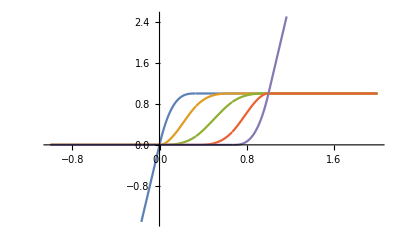

```mathematica
deg=2; (*M-spline basis degree, I-spline degree is deg+1*)
elem=5; (*Number of splines in finished basis*)
knots=Range[0,1,1/(elem-deg)];
knots=Join[ConstantArray[knots[[1]],deg],knots,ConstantArray[knots[[-1]],deg]];
Table[Integrate[BSplineBasis[{deg,knots},i,x],x],{i,0,Length[knots]-deg-2}];
ReplacePart[%,
{{1,1,1,1}->BSplineBasis[{deg,knots},0,0]x,{-1,1}->Join[%[[-1,1]] ,{{(%[[-1]]/.x->1)+BSplineBasis[{deg,knots},Length[knots]-deg-2,1](x-1),x>1}}]}];
(basis=%/%[[All,2]]//Simplify);
Plot[Evaluate[basis],{x,-1,2}]
transform[phi_,a_]:=First[a]+basis.Rest[a]/.{x->phi}
```

#### Bulk import GE results

```mathematica
geWD=StringJoin["/Users/keitokiddo/Dropbox (UFL)/VC_revision/GE/", fl];
SetDirectory[geWD];
```

```mathematica
geprefix=fl;
```

```mathematica
schemes = {"random", "noised", "mut"};
```

```mathematica
names =StringJoin[fl, "_", #,"_"]&/@schemes;
```

```mathematica
pdsGE=Table[{},nschemes,nrep, Length[trs]];
```

```mathematica
Do[pdsGE[[k]][[i,j]]=Module[{y,b,a,yhat,spline,PossibleEffects,FactorMatrix,SortedEffects,Effects,coeffsAll, phige},
b=Transpose[Import[StringReplace["b_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
a=Transpose[Import[StringReplace["a_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
yhat=Transpose[Import[StringReplace["yhat_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
spline[x_]:=transform[x,a];
PossibleEffects=Complement[Join[Tuples[{Range[l],AA}],{{geprefix}}],Thread[{Range[l],Characters[wtAA]}]];
FactorMatrix=Table[Join[{geprefix},Thread[{Range[l],Characters[sequencesAA[[k]]]}]],{k,trs[[j]]}];SortedEffects=SortBy[Transpose[{PossibleEffects,Table[Min[Position[Flatten[FactorMatrix,1],PossibleEffects[[i]]]],{i,Length[PossibleEffects]}]}],Last];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];coeffsAll=MapPartialVal[(FromDigits[#,4]&/@(Effects[[1;;]]/.AAtoDigitRules)) -4+1,b[[2;;]],4*l];
phige = nullonehot.Join[{b[[1]]},coeffsAll];spline/@phige
],{k,3}, {i,nrep},{j,Length@trs}]
```

```mathematica
SetDirectory[StringJoin[wd]];
```

```mathematica
pdsGE>> "pdsGE.m";
```

```mathematica
pdsGE = Import[StringJoin[wd,"/pdsGE.m"]];
```

### Import glmnet results

#### 2way

```mathematica
pds2way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="2way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds2way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### 3way

```mathematica
pds3way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="3way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds3way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

### Combine

```mathematica
pdsAll={pdsVC, pdsGE, pds2way,pds3way};
nmodels=Length[pdsAll];
```

### Plot Random

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

#### Plotting R2 curves

```mathematica
colors={Black,Gray,RGBColor@@({208,209,230}/255),RGBColor@@({51,160,44}/255),RGBColor@@({140,180,227}/255)};
fontsize=20;
fstyle=Table[{GrayLevel[.3],Thickness[.006]},4];
pt=.2;
style={#,Thickness[.004],PointSize[pt]}&/@colors;
```

```mathematica
modellabs={Style["VC regression",FontFamily->"Helvetica"],
Style["Global epistasis",FontFamily->"Helvetica"],
Style["Pairwise regression",FontFamily->"Helvetica"],
Style["Three-way regression",FontFamily->"Helvetica"]};
```

```mathematica
(*modellabs={Style["VC regression",FontFamily->"Helvetica"],
Style["Additive",FontFamily->"Helvetica"],
Style["Global epistasis",FontFamily->"Helvetica"],
Style["Pairwise",FontFamily->"Helvetica"],
Style["Three-way",FontFamily->"Helvetica"]};
modelnames={"VC regression","Additive","Global epistasis","Pairwise","Three-way"};*)
```

```mathematica
pds=pdsAll[[All, 1]];
```

```mathematica
R2s=Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

```mathematica
plotdat=Table[Table[{Around[proportions[[j]],0],Around[Mean[R2s[[k]][[All,j]]],StandardDeviation[R2s[[k]][[All,j]]]]},{j,Length[proportions]}],{k,nmodels}];
```

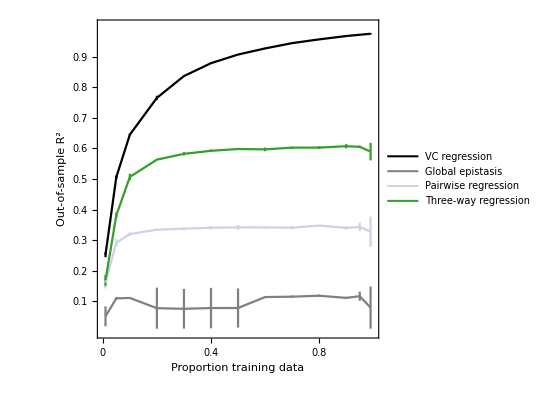

```mathematica
figRandR2=ListPlot[
plotdat,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->True,
ClippingStyle->None,
ImageSize->400,PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.75,.25}]]
```

Add more points between 1 and 10 percent

### Plot noised

#### Reconstruction of training data under noise

```mathematica
pds=pdsAll[[All,2]];
```

```mathematica
R2s=Table[r2[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

```mathematica
MSEs=Table[mse[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

```mathematica
plotdat=Table[Table[{Around[proportions[[j]],0],Around[Median[R2s[[k]][[All,j]]],StandardDeviation[R2s[[k]][[All,j]]]]},{j,Length[proportions]}],{k,nmodels}];
```

```mathematica
modellabs={Style["VC regression",FontFamily->"Helvetica"],
Style["Global epistasis",FontFamily->"Helvetica"],
Style["Pairwise regression",FontFamily->"Helvetica"],
Style["Three-way regression",FontFamily->"Helvetica"]};
```

```mathematica
style={{GrayLevel[0],Thickness[0.004],PointSize[0.2]},{GrayLevel[0.5],Thickness[0.004],PointSize[0.2]},{RGBColor[Rational[208, 255], Rational[209, 255], Rational[46, 51]],Thickness[0.004],PointSize[0.2]},{RGBColor[Rational[1, 5], Rational[32, 51], Rational[44, 255]],Thickness[0.004],PointSize[0.2]},{RGBColor[Rational[28, 51], Rational[12, 17], Rational[227, 255]],Thickness[0.004],PointSize[0.2]}};
```

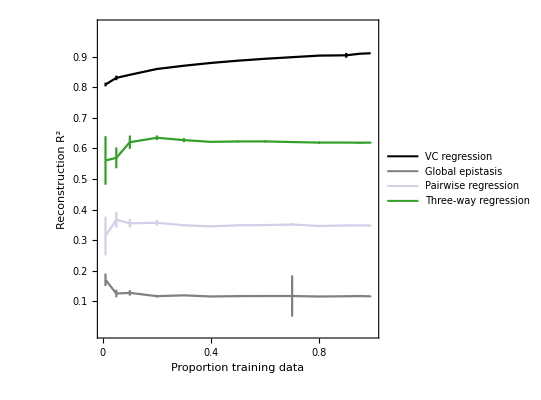

```mathematica
figNoiseR2=ListPlot[
plotdat,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Reconstruction "Superscript[R,2]},
Joined->True,
ClippingStyle->None,
ImageSize->400,PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.75,.25}]]
```

### Plot mut

```mathematica
pds=pdsAll[[All,3]];
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,lg@seqsbyD}];
```

```mathematica
j=2;
proportions[[j]]//N
ttsmut[[j]]//Length
tstbyD=Table[Intersection[ttsmut[[j]],seqbyhd[[d]]], {d, l+1}];
```

0.0500031

62259

```mathematica
Length/@tstbyD;
 %/mks//N;
trsdensity = 1-%
```

{1.,1.,1.,0.876323,0.218519,0.0263081,0.00357633,0.00028578,0.}

```mathematica
Position[#=={}&/@tstbyD,False][[1]]//First ;
dmin=%-1
```

3

```mathematica
R2s=Table[r2[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
```

```mathematica
plotdat=Table[{Around[d,0],Around[Mean[R2s[[k]][[d+1]]],StandardDeviation[R2s[[k]][[d+1]]]]},{k,nmodels},{d,dmin,l}];
```

```mathematica
plotsampling=ListPlot[trsdensity,
BaseStyle->{FontSize->fontsize},
DataRange->{0,l},
PlotRange->{{0,l},{0,1}},
Frame->True,
PlotStyle->{GrayLevel[0],Thickness[0.004],PointSize[0.02]},
FrameStyle->fstyle,
FrameTicks->{{Range[0,1,.1],False},{Range[0,l],False}},FrameLabel->{"Distance to WT","Sampling density"},
PlotRangeClipping->False,
AspectRatio->.75,
ImageSize->400];
```

```mathematica
plotr2d=ListPlot[
plotdat,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,l},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{Range[0,l],False}},FrameLabel->{"Hamming Distance to WT","Out-of-sample "Superscript[R,2]},
Joined->True,
PlotRangeClipping->False,
ImageSize->400,PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.75,.25}]];
```

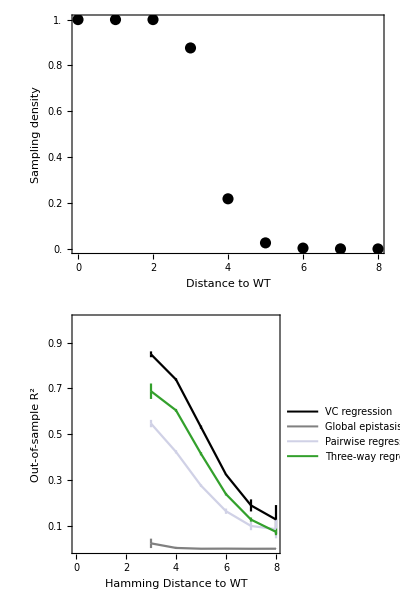

```mathematica
figMutR2=Grid[{{plotsampling},{plotr2d}}]
```

```mathematica
TableForm[{{Superscript[alpha,l]}, {"Dense"}}]
```

4^8
Dense

```mathematica
fig=Labeled[Grid[{{figRandR2},{figNoiseR2},{figMutR2}},Spacings->{1, 3}],Style[Superscript[4,8]
"Dense ",{FontFamily->"Helvetica", FontSize->20,GrayLevel[.4]}], Top]
```

-Graphics-
-Graphics-
-Graphics-Dense  4^8

```mathematica
Export[StringJoin["../figs/", fl, ".m"], fig]
```

../figs/4_8_DEN.m